```mathematica
(*Import packages*)
$LoadFeynArts = True;
$FeynCalcStartupMessages = False;
<< FeynCalc`
$FAVerbose = 0;
AppendTo[$Path, "C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\include"];
<< XSec`
<< TreeLevel`
<< CalcTools`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

CT::shdw: Symbol CT appears in multiple contexts {CalcTools`,Global`}; definitions in context CalcTools` may shadow or be shadowed by other definitions.

## Square amplitudes

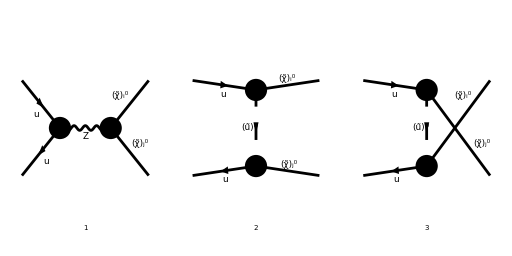

```mathematica
treeDiagrams = InsertFields[
CreateTopologies[0, 2->2,ExcludeTopologies->{Boxes,SelfEnergies,Tadpoles}], 
{F[3, {1,a}], -F[3, {1,b}]} -> {F[11, {i}], F[11, {j}]},
 InsertionLevel -> {Classes},
 Model -> MSSMQCD,
Restrictions->{NoLightFHCoupling,NoElectronHCoupling},
ExcludeParticles->{F[11],F[12],S[1],S[2],S[3],S[4]}
];
Paint[treeDiagrams, Numbering->Simple, ImageSize->{512,256}];
```

```mathematica
Subscript[M, 0][0]=FCFAConvert[
CreateFeynAmp[treeDiagrams], 
IncomingMomenta->{p1,p2}, OutgoingMomenta->{pi,pj},
ChangeDimension->D,
UndoChiralSplittings->True,
List->True,
SMP->True,
DropSumOver->True,
LorentzIndexNames->{μ,ν}
]/.AmpSimplifyRules/.{IndexDelta->FeynCalc`IndexDelta};
```

```mathematica
temp=SMP["g_W"]^2 FeynCalc`IndexDelta[a,b];
```

```mathematica
Subscript[M, 0][1]=temp*DiracSimplify/@(Subscript[M, 0][0]/temp/.ZSimplifyRules/.QSimplifyRules);
Subscript[M, 0][2]=Subscript[M, 0][1]/.{Conjugate[Opp[i_,j_,L]]->-Opp[i,j,R]}//.SuperChargeRules;
```

```mathematica
MakeBoxes[DSf[s_,t_,g_],TraditionalForm]:=SubscriptBox["Δ",MakeBoxes[s,TraditionalForm]]
MakeBoxes[DSfC[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"*"]
MakeBoxes[FeynCalc`Index[Sfermion,a_],TraditionalForm]:=MakeBoxes[a,TraditionalForm]

MakeBoxes[Den[p2_,m2_],TraditionalForm]:=MakeBoxes[1/(p2-m2),TraditionalForm]
MakeBoxes[tMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"t"]
MakeBoxes[uMass[s_,t_,g_],TraditionalForm]:=SubsuperscriptBox["Δ",MakeBoxes[s,TraditionalForm],"u"]
```

```mathematica
Subscript[M, s][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],1]];
Subscript[M, t][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],2]]/.MSf[a_,t_,g_]^2->DSf[a,t,g]/.Index[Sfermion,5]->Index[Sfermion,A];
Subscript[M, u][0]=FeynAmpDenominatorExplicit[Part[Subscript[M, 0][2],3]]/.MSf[a_,t_,g_]^2->DSf[a,t,g]/.Index[Sfermion,5]->Index[Sfermion,A];
```

```mathematica
Subscript[M̄, s][0]=ConjugateAmplitude[Subscript[M, s][0]];
Subscript[M̄, t][0]=ConjugateAmplitude[Subscript[M, t][0]];
Subscript[M̄, u][0]=ConjugateAmplitude[Subscript[M, u][0]];
```

```mathematica
(*Common prefactor for the squared amplitudes.*)
Prefactor=4 (FeynCalc`IndexDelta[a,b])^2 SMP["g_W"]^4;
```

```mathematica
(*Square the amplitudes*)
Subscript[I, ss][0]=SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, s][0]];
Subscript[I, tt][0]=SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, t][0]/.A->B];
Subscript[I, uu][0]=SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, u][0]/.A->B];
Subscript[I, st][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, t][0]]+SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, s][0]])/2;
Subscript[I, su][0]=(SquareAmplitudes[Subscript[M, s][0],Subscript[M̄, u][0]]+SquareAmplitudes[Subscript[M, u][0],Subscript[M̄, s][0]])/2;
Subscript[I, tu][0]=(SquareAmplitudes[Subscript[M, t][0],Subscript[M̄, u][0]/.A->B]+SquareAmplitudes[Subscript[M, u][0]/.A->B,Subscript[M̄, t][0]])/2;
```

```mathematica
(*Function for taking the limit D->4 of an expression.*)
FixDimension[amp_]:=(SelectFree2[#1,Eps]&)[
ChangeDimension[amp,4]/.{D->4}//FeynAmpDenominatorExplicit//DiracSimplify//Simplify
];
```

```mathematica
(*Function for collecting the available kinemtic terms.*)
IsolateKinematicTerms={
(t-MNeu[i])(t-MNeu[j])->KT[1],
(u-MNeu[i])(u-MNeu[j])->KT[2],
MNeu[i]MNeu[j]s->KT[3]};
KinematicTerms={KT[1],KT[2],KT[3]};
FreeKinematicTerms={
KT[1]->(t-MNeu[i])(t-MNeu[j]),
KT[2]->(u-MNeu[i])(u-MNeu[j]),
KT[3]->MNeu[i]MNeu[j]s};
CollectTerms[amp_]:=Collect2[ReduceMandelstam[amp]/.IsolateKinematicTerms,KinematicTerms]/.FreeKinematicTerms
```

```mathematica
(*Function for converting propagator denominators to a Den-function with Breit-Wigner mass replacements.*)
Convert2Den={
t-DSf[args__]->1/Den[t,DSf[args]],
u-DSf[args__]->1/Den[u,DSf[args]],
t-DSfC[args__]->1/Den[t,DSfC[args]],
u-DSfC[args__]->1/Den[u,DSfC[args]],
s-SMP["m_Z"]^2->1/Den[s,SMP["m_Z"]^2]
};
DenominatorFactors={
Den[t,m1_]Den[u,m2_],
Den[s,m1_]Den[u,m2_],
Den[s,m1_]Den[t,m2_]
};
FactorDenominators[expr_]:=Prefactor Collect[
FixDimension[(expr/Prefactor)/.Convert2Den]//Expand,
DenominatorFactors,
CollectTerms
]
```

```mathematica
(*Substitute the propagator factors.*)
Subscript[I, ss][1]=FactorDenominators[Subscript[I, ss][0]]
Subscript[I, tt][1]=FactorDenominators[Subscript[I, tt][0]]
Subscript[I, uu][1]=FactorDenominators[Subscript[I, uu][0]]
Subscript[I, st][1]=FactorDenominators[Subscript[I, st][0]]
Subscript[I, su][1]=FactorDenominators[Subscript[I, su][0]]
Subscript[I, tu][1]=FactorDenominators[Subscript[I, tu][0]]
```

4 g_W^4 δ_ab^2 ((1/(s-m_Z^2))^2 (Z_s^L Conjugate[(Z_s^L)]+Z_s^R Conjugate[(Z_s^R)]) (2 m_i^2 m_j^2-t m_i^2-u m_i^2-t m_j^2-u m_j^2+t^2+u^2)-s m_i m_j (1/(s-m_Z^2))^2 ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2))

4 g_W^4 δ_ab^2 (t-m_i^2) (t-m_j^2) 1/(t-Δ_SfeA) 1/(t-Δ_SfeB^*) (Q_SfeA^(L L̄) Conjugate[(Q_SfeB^(L L̄))]+Q_SfeB^(R R̄) Conjugate[(Q_SfeA^(R R̄))]+Q_SfeA^LR Conjugate[(Q_SfeB^LR)]+Q_SfeB^RL Conjugate[(Q_SfeA^RL)])

4 g_W^4 δ_ab^2 (u-m_i^2) (u-m_j^2) 1/(u-Δ_SfeA) 1/(u-Δ_SfeB^*) (Q_SfeB^(L L̄) Conjugate[(Q_SfeA^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^RL Conjugate[(Q_SfeB^RL)]+Q_SfeB^LR Conjugate[(Q_SfeA^LR)])

4 g_W^4 δ_ab^2 (1/(s-m_Z^2) 1/(t-Δ_SfeA) (1/2 (t-m_i^2) (t-m_j^2) (Z_s^R Conjugate[(Q_SfeA^(R R̄))]+Z_s^L Q_SfeA^(L L̄))-1/2 s m_i m_j (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))]))+1/(s-m_Z^2) 1/(t-Δ_SfeA^*) (1/2 (t-m_i^2) (t-m_j^2) (Conjugate[(Z_s^L)] Conjugate[(Q_SfeA^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])-1/2 s m_i m_j (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Q_SfeA^(R R̄))))

4 g_W^4 δ_ab^2 (1/(s-m_Z^2) 1/(u-Δ_SfeA^*) (1/2 (u-m_i^2) (u-m_j^2) (Z_s^R Conjugate[(Q_SfeA^(R R̄))]+Z_s^L Q_SfeA^(L L̄))-1/2 s m_i m_j (Q_SfeA^(L L̄) Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Conjugate[(Q_SfeA^(R R̄))]))+1/(s-m_Z^2) 1/(u-Δ_SfeA) (1/2 (u-m_i^2) (u-m_j^2) (Conjugate[(Z_s^L)] Conjugate[(Q_SfeA^(L L̄))]+Q_SfeA^(R R̄) Conjugate[(Z_s^R)])-1/2 s m_i m_j (Z_s^L Conjugate[(Q_SfeA^(L L̄))]+Z_s^R Q_SfeA^(R R̄))))

4 g_W^4 δ_ab^2 (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (1/2 (t u-m_i^2 m_j^2) (Q_SfeA^LR Conjugate[(Q_SfeB^RL)]+Q_SfeB^LR Conjugate[(Q_SfeA^RL)])-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)))+1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB) (1/2 (t u-m_i^2 m_j^2) (Q_SfeA^RL Conjugate[(Q_SfeB^LR)]+Q_SfeB^RL Conjugate[(Q_SfeA^LR)])-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄))))

```mathematica
(*Temporary variables for the expanded kinematic terms.*)
tij=((t-MNeu[i]^2)(t-MNeu[j]^2))//Expand;
uij=((u-MNeu[i]^2)(u-MNeu[j]^2))//Expand;
```

```mathematica
(*Add squared amplitudes together, omitting prefactor and prettifying kinematic terms.*)
Itot[0]=(Subscript[I, ss][1]+Subscript[I, tt][1]+Subscript[I, uu][1]+2 Subscript[I, st][1]+2 Subscript[I, su][1]+2 Subscript[I, tu][1])/Prefactor;
Itot[1]=Itot[0]/.{tij+uij->(t-MNeu[i]^2)(t-MNeu[j]^2)+(u-MNeu[i]^2)(u-MNeu[j]^2)}
```

1/(4 δ_ab^2 g_W^4)(4 1/(u-Δ_SfeA) 1/(u-Δ_SfeB^*) δ_ab^2 (u-m_i^2) (u-m_j^2) (Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) g_W^4+4 1/(t-Δ_SfeA) 1/(t-Δ_SfeB^*) δ_ab^2 (t-m_i^2) (t-m_j^2) (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) g_W^4+8 δ_ab^2 (1/(t-Δ_SfeA) 1/(u-Δ_SfeB^*) (1/2 (t u-m_i^2 m_j^2) (Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)))+1/(t-Δ_SfeA^*) 1/(u-Δ_SfeB) (1/2 (t u-m_i^2 m_j^2) (Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄)))) g_W^4+4 δ_ab^2 ((1/(s-m_Z^2))^2 ((t-m_i^2) (t-m_j^2)+(u-m_i^2) (u-m_j^2)) (Conjugate[(Z_s^L)] Z_s^L+Conjugate[(Z_s^R)] Z_s^R)-s (1/(s-m_Z^2))^2 m_i m_j ((Conjugate[(Z_s^L)])^2+(Conjugate[(Z_s^R)])^2+(Z_s^L)^2+(Z_s^R)^2)) g_W^4+8 δ_ab^2 (1/(s-m_Z^2) 1/(t-Δ_SfeA) (1/2 (t-m_i^2) (t-m_j^2) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)))+1/(s-m_Z^2) 1/(t-Δ_SfeA^*) (1/2 (t-m_i^2) (t-m_j^2) (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄))-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R))) g_W^4+8 δ_ab^2 (1/(s-m_Z^2) 1/(u-Δ_SfeA^*) (1/2 (u-m_i^2) (u-m_j^2) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)-1/2 s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)))+1/(s-m_Z^2) 1/(u-Δ_SfeA) (1/2 (u-m_i^2) (u-m_j^2) (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄))-1/2 s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R))) g_W^4)

```mathematica
(*Show that the total amplitude can be written as effective charges in front of these four kinematic terms.*)
Collect[
Itot[1],
{s*MNeu[i]*MNeu[j],(t-MNeu[i]^2)(t-MNeu[j]^2),(u-MNeu[i]^2)(u-MNeu[j]^2),t*u-MNeu[i]^2*MNeu[j]^2},
(Isolate[#1//Simplify,IsolateNames->Q]&)
]
```

Q(2002) s m_i m_j+Q(2010) (t u-m_i^2 m_j^2)+Q(2007) (t-m_i^2) (t-m_j^2)+Q(2009) (u-m_i^2) (u-m_j^2)

## Integrate over t

```mathematica
(*To simplify before integrating over t, we will need to convert all terms containing u to t.*)
Itot[2]=Collect[
Itot[1]/.{Den[u,DSf[args__]]->-Den[t,uMass[args]],Den[u,DSfC[args__]]->-Den[t,uMass[args]*],Den[t,DSf[args__]]->Den[t,tMass[args]],Den[t,DSfC[args__]]->Den[t,tMass[args]*]}/.{u->MNeu[i]^2+MNeu[j]^2-s-t}//Expand,
Den[args1__]Den[args2__],
Simplify
]
```

(-s m_i m_j (Conjugate[(Z_s^L)])^2+(s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t)) Z_s^L Conjugate[(Z_s^L)]-s (Conjugate[(Z_s^R)])^2 m_i m_j+Conjugate[(Z_s^R)] (s^2+2 t s+2 t^2-(s+2 t) m_j^2-m_i^2 (-2 m_j^2+s+2 t)) Z_s^R-s m_i m_j ((Z_s^L)^2+(Z_s^R)^2)) (1/(s-m_Z^2))^2+1/(t-Conjugate[(Δ_SfeA^t)]) (Conjugate[(Q_SfeA^(L L̄))] (Conjugate[(Z_s^L)] (t-m_i^2) (t-m_j^2)-s m_i m_j Z_s^L)+Q_SfeA^(R R̄) (Conjugate[(Z_s^R)] (t-m_i^2) (t-m_j^2)-s m_i m_j Z_s^R)) 1/(s-m_Z^2)+1/(t-Δ_SfeA^u) (Conjugate[(Q_SfeA^(L L̄))] (s m_i m_j Z_s^L-Conjugate[(Z_s^L)] (-m_i^2+s+t) (-m_j^2+s+t))+Q_SfeA^(R R̄) (s m_i m_j Z_s^R-Conjugate[(Z_s^R)] (-m_i^2+s+t) (-m_j^2+s+t))) 1/(s-m_Z^2)+1/(t-Δ_SfeA^t) (-Q_SfeA^(L L̄) (s Conjugate[(Z_s^L)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^L)-Conjugate[(Q_SfeA^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(t-m_i^2) (t-m_j^2) Z_s^R)) 1/(s-m_Z^2)+1/(t-Conjugate[(Δ_SfeA^u)]) (Q_SfeA^(L L̄) (s Conjugate[(Z_s^L)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^L)+Conjugate[(Q_SfeA^(R R̄))] (s Conjugate[(Z_s^R)] m_i m_j-(-m_i^2+s+t) (-m_j^2+s+t) Z_s^R)) 1/(s-m_Z^2)+1/(t-Conjugate[(Δ_SfeB^u)]) 1/(t-Δ_SfeA^u) (-m_i^2+s+t) (-m_j^2+s+t) (Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))+1/(t-Conjugate[(Δ_SfeB^u)]) 1/(t-Δ_SfeA^t) (Conjugate[(Q_SfeA^RL)] Q_SfeB^LR t^2-Conjugate[(Q_SfeA^RL)] m_i^2 Q_SfeB^LR t-Conjugate[(Q_SfeA^RL)] m_j^2 Q_SfeB^LR t+s Conjugate[(Q_SfeA^RL)] Q_SfeB^LR t+s Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))] m_i m_j+Conjugate[(Q_SfeB^RL)] ((m_j^2-t) m_i^2+t (-m_j^2+s+t)) Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] m_i^2 m_j^2 Q_SfeB^LR+s m_i m_j Q_SfeA^(L L̄) Q_SfeB^(L L̄))+1/(t-Conjugate[(Δ_SfeB^t)]) 1/(t-Δ_SfeA^t) (t-m_i^2) (t-m_j^2) (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄))+1/(t-Conjugate[(Δ_SfeA^t)]) 1/(t-Δ_SfeB^u) (Conjugate[(Q_SfeA^LR)] Q_SfeB^RL t^2-Conjugate[(Q_SfeA^LR)] m_i^2 Q_SfeB^RL t-Conjugate[(Q_SfeA^LR)] m_j^2 Q_SfeB^RL t+s Conjugate[(Q_SfeA^LR)] Q_SfeB^RL t+s Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))] m_i m_j+Conjugate[(Q_SfeB^LR)] ((m_j^2-t) m_i^2+t (-m_j^2+s+t)) Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] m_i^2 m_j^2 Q_SfeB^RL+s m_i m_j Q_SfeA^(R R̄) Q_SfeB^(R R̄))

```mathematica
(*Convert all t-dependence to a dictionary of standard t-integrals Subscript[T, d]^p(Subscript[Δ, 1],...,Subscript[Δ, d]).*)
ItotIntegrals[0]=ToTIntegrals[Itot[2]]
ItotIntegrals[1]=ReduceTIntegrals[ToTIntegrals[Itot[2]]]
```

CT(2043) T_2^0(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])-CT(2051) T_2^1(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+CT(2042) T_2^2(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+CT(2041) T_2^0(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(2045) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(2050) T_2^1(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(2053) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(2049) T_2^2(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+CT(2052) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+CT(2047) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(2054) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(2046) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+CT(2020) T_1^0(Conjugate[(Δ_SfeA^t)])-CT(2036) T_1^1(Conjugate[(Δ_SfeA^t)])+CT(2039) T_1^2(Conjugate[(Δ_SfeA^t)])+CT(2025) T_1^0(Conjugate[(Δ_SfeA^u)])-CT(2059) T_1^1(Conjugate[(Δ_SfeA^u)])-CT(2061) T_1^2(Conjugate[(Δ_SfeA^u)])+CT(2029) T_1^0(Δ_SfeA^t)-CT(2060) T_1^1(Δ_SfeA^t)+CT(2061) T_1^2(Δ_SfeA^t)+CT(2033) T_1^0(Δ_SfeA^u)-CT(2038) T_1^1(Δ_SfeA^u)-CT(2039) T_1^2(Δ_SfeA^u)+CT(2016) T_0^0+2 CT(2056) T_0^1+2 CT(2057) T_0^2

CT(2069) T_1^0(Conjugate[(Δ_SfeA^t)])+CT(2077) T_1^0(Conjugate[(Δ_SfeA^u)])+CT(2083) T_1^0(Δ_SfeA^t)+CT(2086) T_1^0(Δ_SfeA^u)+CT(2071) T_1^0(Conjugate[(Δ_SfeB^t)])+CT(2080) T_1^0(Conjugate[(Δ_SfeB^u)])+CT(2065) T_0^0+2 CT(2056) T_0^1+2 CT(2057) T_0^2

```mathematica
(*We can write it out in terms of the basic charges using GetKinematicCoefficients.*)
Collect[ItotIntegrals[0],tIntegral[args__],GetKinematicCoefficients]
```

((-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_i^2+(-2 Abs[Z_s^L]^2-2 Abs[Z_s^R]^2) m_j^2+s (2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2)) T_0^1 (1/(s-m_Z^2))^2+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) T_0^2 (1/(s-m_Z^2))^2+T_0^0 ((Abs[Z_s^L]^2+Abs[Z_s^R]^2) s^2+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_i^2 s+(-Abs[Z_s^L]^2-Abs[Z_s^R]^2) m_j^2 s+m_i m_j (-(Conjugate[(Z_s^L)])^2-(Conjugate[(Z_s^R)])^2-(Z_s^L)^2-(Z_s^R)^2) s+(2 Abs[Z_s^L]^2+2 Abs[Z_s^R]^2) m_i^2 m_j^2) (1/(s-m_Z^2))^2+((-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄))) T_1^1(Conjugate[(Δ_SfeA^t)]) 1/(s-m_Z^2)+((Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_i^2+s (-2 Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-2 Conjugate[(Z_s^R)] Q_SfeA^(R R̄))+m_j^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄))) T_1^1(Δ_SfeA^u) 1/(s-m_Z^2)+(Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) T_1^2(Conjugate[(Δ_SfeA^t)]) 1/(s-m_Z^2)+(-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) T_1^2(Δ_SfeA^u) 1/(s-m_Z^2)+T_1^2(Conjugate[(Δ_SfeA^u)]) (-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R) 1/(s-m_Z^2)+T_1^2(Δ_SfeA^t) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) 1/(s-m_Z^2)+T_1^1(Δ_SfeA^t) ((-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_i^2+m_j^2 (-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R)) 1/(s-m_Z^2)+T_1^1(Conjugate[(Δ_SfeA^u)]) ((Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_i^2+s (-2 Q_SfeA^(L L̄) Z_s^L-2 Conjugate[(Q_SfeA^(R R̄))] Z_s^R)+m_j^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R)) 1/(s-m_Z^2)+T_1^0(Conjugate[(Δ_SfeA^u)]) ((-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s^2+m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)) s+m_i^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s+m_j^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) s+m_i^2 m_j^2 (-Q_SfeA^(L L̄) Z_s^L-Conjugate[(Q_SfeA^(R R̄))] Z_s^R)) 1/(s-m_Z^2)+T_1^0(Δ_SfeA^t) (m_i^2 (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R) m_j^2+s m_i (-Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]-Conjugate[(Z_s^L)] Q_SfeA^(L L̄)) m_j) 1/(s-m_Z^2)+T_1^0(Conjugate[(Δ_SfeA^t)]) (m_i^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) m_j^2+s m_i (-Conjugate[(Q_SfeA^(L L̄))] Z_s^L-Q_SfeA^(R R̄) Z_s^R) m_j) 1/(s-m_Z^2)+T_1^0(Δ_SfeA^u) ((-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s^2+m_i^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s+m_j^2 (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) s+m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R) s+m_i^2 m_j^2 (-Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]-Conjugate[(Z_s^R)] Q_SfeA^(R R̄))) 1/(s-m_Z^2)+(m_i^2 (Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) m_j^2+s m_i (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄)) m_j) T_2^0(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+m_i^2 m_j^2 (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) T_2^0(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+(m_i^2 (Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) m_j^2+s m_i (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)) m_j) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+((Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) s^2+m_i^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) s+m_j^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) s+m_i^2 m_j^2 (Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))) T_2^0(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+((-Conjugate[(Q_SfeB^LR)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^LR)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^RL)+s (Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL)) T_2^1(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+((-Conjugate[(Q_SfeB^LR)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^RL-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^LR)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^RL-Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)-Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄))) T_2^1(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+((-Conjugate[(Q_SfeB^RL)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^LR-Conjugate[(Q_SfeA^RL)] Q_SfeB^LR)+s (Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR)) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+((-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) m_i^2+m_j^2 (-Conjugate[(Q_SfeB^RL)] Q_SfeA^RL-Conjugate[(Q_SfeA^LR)] Q_SfeB^LR-Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)-Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))+s (2 Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+2 Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+2 Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+2 Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄))) T_2^1(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])+(Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) T_2^2(Conjugate[(Δ_SfeA^t)],Conjugate[(Δ_SfeB^u)])+(Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) T_2^2(Conjugate[(Δ_SfeB^t)],Conjugate[(Δ_SfeA^t)])+(Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^t)])+(Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) T_2^2(Conjugate[(Δ_SfeB^u)],Conjugate[(Δ_SfeA^u)])

```mathematica
(*A function for collecting all effective charges in an expression.*)
EffectiveCharges={
Qtu[args1__]Qtu[args2__],
Qtu[args1__]Qtu[args2__]*,
Qtu[args1__]*Qtu[args2__]*,
QtuC[args1__]QtuC[args2__],
QtuC[args1__]QtuC[args2__]*,
QtuC[args1__]*QtuC[args2__]*,
Zs[arg_]QtuC[args__],
Zs[arg_]*QtuC[args__],
Zs[arg_]QtuC[args__]*,
Zs[arg_]*QtuC[args__]*
};
CollectEffCharges[expr_]:=Collect2[
Collect[
FRH[expr]//Expand,
EffectiveCharges,
(Isolate[#1//Simplify]&)
],
KK[arg_]
]
```

```mathematica
(*Write out the analytic results of all the Subscript[T, d]^p-integrals and collect into the possible terms dependent on the t-limits t1 and t0.*)
ItotIntegrals[2]=Collect[
FreeTIntegrals[ItotIntegrals[0]],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(2112) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(2118) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(2133) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(2140) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+KK(2144) log((t1-Conjugate[(Δ_SfeB^t)])/(t0-Conjugate[(Δ_SfeB^t)]))+KK(2150) log((t1-Conjugate[(Δ_SfeB^u)])/(t0-Conjugate[(Δ_SfeB^u)]))+KK(2155) log((t1-Δ_SfeB^u)/(t0-Δ_SfeB^u))+2/3 KK(2099) (t1^3-t0^3)+KK(2098) (t1^2-t0^2)+KK(2095) (t1-t0)+KK(2161)

```mathematica
(*Collect terms that can combine under A<->B.*)
BindexLogs={
Log[(t1-tMass[Index[Sfermion,B],args__]*)/(t0-tMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__]*)/(t0-uMass[Index[Sfermion,B],args__]*)],
Log[(t1-uMass[Index[Sfermion,B],args__])/(t0-uMass[Index[Sfermion,B],args__])]
};
ItotIntegrals[3]=Collect[
((((SelectNotFree[ItotIntegrals[2],BindexLogs])//FRH)/.A->C)/.{B->A,C->B})+SelectFree[ItotIntegrals[2],BindexLogs],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(2164) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(2171) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(2133) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(2177) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+2/3 KK(2099) (t1^3-t0^3)+KK(2098) (t1^2-t0^2)+KK(2095) (t1-t0)+KK(2161)

```mathematica
(*Conjugate total expression to assert if result is real.*)
ItotIntegralsC[0]=Refine[
Collect[
ItotIntegrals[3]//FRH,
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Conjugate[#1]//.{Conjugate[a_+b_]->a*+b*,Conjugate[a_*b_]->a*b*}&)
]/.{Log[arg_]->Log[arg*]},
Assumptions->{t1∈Reals,t0∈Reals,Den[s,SMP["m_Z"]^2]∈Reals,MNeu[i_]∈Reals,s∈Reals}
];
ItotIntegralsC[1]=Collect[
ItotIntegralsC[0]//Expand,
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Isolate[CollectEffCharges[#1]]&)
]
```

KK(2164) log((t1-Conjugate[(Δ_SfeA^t)])/(t0-Conjugate[(Δ_SfeA^t)]))+KK(2171) log((t1-Conjugate[(Δ_SfeA^u)])/(t0-Conjugate[(Δ_SfeA^u)]))+KK(2337) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t))+KK(2336) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u))+KK(2339)

```mathematica
FCCompareResults[FRH[ItotIntegrals[3]],FRH[ItotIntegralsC[1]],Text->{"\tResult is analytically real:","CORRECT.","WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
```

Result is analytically real: CORRECT.

```mathematica
ItotIntegrals[4]=ItotIntegrals[3]//.{a_*Log[(t1-tMass[args__])/(t0-tMass[args__])]+b_*Log[(t1-tMass[args__]*)/(t0-tMass[args__]*)]->2Re[a*Log[(t1-tMass[args])/(t0-tMass[args])]],a_*Log[(t1-uMass[args__])/(t0-uMass[args__])]+b_*Log[(t1-uMass[args__]*)/(t0-uMass[args__]*)]->2Re[a*Log[(t1-uMass[args])/(t0-uMass[args])]]}
```

2 Re(KK(2133) log((t1-Δ_SfeA^t)/(t0-Δ_SfeA^t)))+2 Re(KK(2177) log((t1-Δ_SfeA^u)/(t0-Δ_SfeA^u)))+2/3 KK(2099) (t1^3-t0^3)+KK(2098) (t1^2-t0^2)+KK(2095) (t1-t0)+KK(2161)

```mathematica
(*Substitute the tMass and uMass functions for their actual dependence on masses and decay rates (and s).*)
DeltaSubs={tMass[a_,args__]->MSf[a,args]^2+ⅈ*Subscript[Γ, a] MSf[a,args],uMass[a_,args__]->MNeu[i]^2+MNeu[j]^2-s-MSf[a,args]^2-ⅈ*Subscript[Γ, a] MSf[a,args]};
DeltaAssumptions={MNeu[i_]∈Reals,MSf[args__]∈Reals,Subscript[Γ, a_]∈Reals,s∈Reals};
Collect[
FRH[ItotIntegrals[4]],
{t1-t0,t1^2-t0^2,t1^3-t0^3,Log[arg_]},
(Simplify[#1/.DeltaSubs,Assumptions->DeltaAssumptions]&)
]/.{Den[s_,m_]->1/(s-m)}
```

-((t0-t1) (-m_i^2-m_j^2+2 m_((q̃)_SfeA)^2+s) (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)))/(s-m_Z^2)+2 Re(log((-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t1)/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+t0)) (-(s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Z_s^R)]+Conjugate[(Z_s^L)] Q_SfeA^(L L̄)))/(s-m_Z^2)+((m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))/(s-m_Z^2)+((Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(-m_((q̃)_SfeA)^2-ⅈ Γ_SfeA m_((q̃)_SfeA)+m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))+(s m_i m_j (Conjugate[(Q_SfeA^(R R̄))] Conjugate[(Q_SfeB^(R R̄))]+Q_SfeA^(L L̄) Q_SfeB^(L L̄)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)))+2 Re(log((-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t1+ⅈ m_((q̃)_SfeA) Γ_SfeA)/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+s+t0+ⅈ m_((q̃)_SfeA) Γ_SfeA)) (-(s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Q_SfeB^(L L̄))]+Q_SfeA^(R R̄) Q_SfeB^(R R̄)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)+((Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(s-m_Z^2)+(s m_i m_j (Conjugate[(Q_SfeA^(L L̄))] Z_s^L+Q_SfeA^(R R̄) Z_s^R))/(s-m_Z^2)+((Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)) (m_i^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) (m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)-m_j^2))/(m_((q̃)_SfeA)^2+ⅈ Γ_SfeA m_((q̃)_SfeA)-m_((q̃)_SfeB) (m_((q̃)_SfeB)-ⅈ Γ_SfeB))-((Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL) ((m_j^2-m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA)) m_i^2+m_((q̃)_SfeA) (m_((q̃)_SfeA)+ⅈ Γ_SfeA) (-m_j^2+m_((q̃)_SfeA)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA)))/(-m_i^2-m_j^2+m_((q̃)_SfeA)^2+m_((q̃)_SfeB)^2+s+ⅈ m_((q̃)_SfeA) Γ_SfeA-ⅈ m_((q̃)_SfeB) Γ_SfeB)))-((t0-t1) (-m_i^2-m_j^2+2 m_((q̃)_SfeA)^2+s) (Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))/(s-m_Z^2)+(2 (t1^3-t0^3) (Conjugate[(Z_s^L)] Z_s^L+Conjugate[(Z_s^R)] Z_s^R))/(3 (s-m_Z^2)^2)+((t1^2-t0^2) (-m_i^2-m_j^2+s) (Conjugate[(Z_s^L)] Z_s^L+Conjugate[(Z_s^R)] Z_s^R))/((s-m_Z^2)^2)+(t1-t0) (Conjugate[(Q_SfeB^LR)] Q_SfeA^LR+Conjugate[(Q_SfeB^RL)] Q_SfeA^LR+Conjugate[(Q_SfeB^LR)] Q_SfeA^RL+Conjugate[(Q_SfeB^RL)] Q_SfeA^RL+Conjugate[(Q_SfeA^LR)] Q_SfeB^LR+Conjugate[(Q_SfeA^RL)] Q_SfeB^LR+Conjugate[(Q_SfeA^LR)] Q_SfeB^RL+Conjugate[(Q_SfeA^RL)] Q_SfeB^RL+Conjugate[(Q_SfeB^(L L̄))] Q_SfeA^(L L̄)+Conjugate[(Q_SfeB^(R R̄))] Q_SfeA^(R R̄)+Conjugate[(Q_SfeA^(L L̄))] Q_SfeB^(L L̄)+Conjugate[(Q_SfeA^(R R̄))] Q_SfeB^(R R̄)-(2 s (Conjugate[(Q_SfeA^(L L̄))] Conjugate[(Z_s^L)]+Conjugate[(Z_s^R)] Q_SfeA^(R R̄)+Q_SfeA^(L L̄) Z_s^L+Conjugate[(Q_SfeA^(R R̄))] Z_s^R))/(s-m_Z^2)+(-s m_i m_j (Conjugate[(Z_s^L)])^2+(s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Z_s^L Conjugate[(Z_s^L)]-s (Conjugate[(Z_s^R)])^2 m_i m_j+Conjugate[(Z_s^R)] (s (s-m_j^2)-m_i^2 (s-2 m_j^2)) Z_s^R-s m_i m_j ((Z_s^L)^2+(Z_s^R)^2))/((s-m_Z^2)^2))

## Write results to file

```mathematica
SetDirectory["C:\\Users\\Bruker\\Documents\\Skole\\master\\masteroppgave\\code\\mathematica\\results"];
Directory[];
```

```mathematica
(*Subscript[I, ss][1]>>Iss.txt
Subscript[I, tt][1]>>Itt.txt
Subscript[I, uu][1]>>Iuu.txt
Subscript[I, st][1]>>Ist.txt
Subscript[I, su][1]>>Isu.txt
Subscript[I, tu][1]>>Itu.txt*)
```